-Graphics-

# Introduction to Probability Theory Bayesian Inference Illustrated by Pass-Fail Trials

## James C. Rock, PhD, PE, CIH

## Outline of Presentation

### Why we need Probability Theory Axioms of Probability Theory Bayes Rule, Marginalization and Evidence The Binary Decision Problem, - Deduction: Probability of M Passes Given N trials and prob = p. - Induction: pdf[p] given M passes observed in N trials. Confidence Interval (frequentist) vs Credible Region (Bayesian) Deductive v Inductive Reasoning Summary

## Why We need Probability Theory

“The actual science of logic is conversant at present only with things either certain, impossible, or entirely doubtful, none of which (fortunately) we have to reason on.  Therefore the true logic for this world is the calculus of Probabilities, which takes account of the magnitude of the probability which is, or ought to be, in a reasonable man’s mind.” 
	James Clerk Maxwell (1850), quoted by Edwin Jaynes (1994).

## Deductive vs. Inductive Logic

### You can reason by deduction if you have axioms to start with, and you can reason by inference if you have data to start with. Deduction finds Lemmas, Theorems and Rules from a few axioms. Abstract Mathematicians live in this world Induction finds a cause from measurements of several effects. Others who learn from mistakes live here

## Probability Theory - LaPlace (1812)

### La théorie des probabilitiés n’est que le bon sens reduit au calcul

1.  Represent probabilities with real numbers.

2.  Qualitative agreement with common sense.

3.  Consistent Answers.

### Probability Theory is nothing but good sense reduced to calculations

## Probability Theory - Cox Desiderata (1946)

### Cox (1946) sought a complete probability theory

1.  If there is more than one way to estimate the probability that a proposition is true, 
all observers with the same information should obtain the same estimate.

2.  When estimating the probability that a proposition is true, 
one also estimates the probability that it is false.

3.  An estimate for the probability that a proposition, Y, is true,
plus an estimate that the probability another proposition, X, is true when Y is true,
quantifies an estimate for the probability that both X and Y are true.

## Probability Axioms Lead to Probability Theory

### Cox (1946) showed his desiderata lead to two unique axioms

SUM RULE:   
	prob[ X | C ] + prob[ X^- |  C ] = 1

PRODUCT RULE:  
	prob[ X, Y | C ] = prob[ X | Y, C ] * prob[ Y | C ]

## Notations Used in Probability Axioms

X and Y are propositions that are true with some probability, 0 ≤ p ≤ 1
“ | ” means “Given”
“ C ” means “Prior Conditions or Information” such as independent trials
“ , ” means Boolean “AND”
“ prob[ X, Y | C ] ” means probability that both X AND Y are true, given C is true
“PDF” means probability distribution function
“LKF” means likelihood function

Note that all probabilities are conditional on some identifiable information.

## Today’s Probability Scale

prob[ any event ] lies in the range {0, 1}

prob[ certain event ] = 1

prob[ impossible event ] = 0

pdf[ z ] has unit area

lkf[ z ] = kk * pdf[ z ];  lkf has area = kk.

NOTE that in general, the product of two or more pdfs is an lkf.

## Bayes Rule from Probability Axioms

### Write the Product Rule for two equivalent propositions

prob[ X, Y | C ] = prob[ X | Y, C ] * prob[ Y | C ]
	prob[ Y, X | C ] = prob[ Y | X, C ] * prob[ X | C ]

#### Ordering of X and Y does not affect probability, so equating the right sides and rearranging yields Bayes Theorem.

prob[ X | Y, C ] = (prob[ Y | X, C ] * prob[ X | C ])/prob[Y|C]

## Bayes Rule for Empirical Science

### Find the Probability an hypothesis is TRUE, given new data

prob[ Hypothesis | Data, C ] = (prob[ Data | Hypothesis, C ] * prob[ Hypothesis | C ])/prob[Data|C]
			          ∝ prob[ Data | Hypothesis, C ] * prob[ Hypothesis | C ]

### Rewrite in terms of PDF and LKF

posteriorPDF = (dataLKF* priorPDF)/Evidence;    posteriorLKF = dataLKF * priorLKF

Evidence is also called Global Likelihood or Marginal Likelihood.  
The term Likelihood has multiple meanings used variously by different authors.

## Bayesian Marginalization from Axioms

### From the Product Rule

prob[ X, Y | C ] = prob[ Y, X | C ] = prob[ Y | X, C ] * prob[ X | C ]

prob[ X, Y^- | C ] = prob[ Y^-, X | C ] = prob[ Y^- | X, C ] * prob[ X | C ]

### Add Leftmost and Rightmost Terms

prob[ X, Y | C ] + prob[ X, Y^- | C ] = 
	( prob[ Y | X, C ] + prob[ Y^- | X, C ] ) * prob[ X | C ]

### From the Sum Rule, The expression in “()” has prob = 1, so

prob[ X, Y | C ] + prob[ X, Y^- | C ] = prob[ X | C ]

### Given n exhaustive and exclusive propositions, Y1 to Yn,

prob[ X | C ] = prob[ X, Y1 | C ] + prob[ X, Y2 | C ] + ... + prob[ X ,Yn | C ]

### When {X, Y} is represented by a continuous (joint) PDF,

pdf [ X | C ] = ∫ pdf [ X, Y | C ] ⅆ Y

## Binomial Likelihood Function (LKF)

Single Trial probabilities:  pass = p ,  fail = (1-p) by SUM RULE

If first trial is pass, then the priorLKF for the second trial = p

In the second trial the LKF = p for a pass, and LKF = (1-p) for a fail
By Bayes Rule, the posterior after 2 trials = LKF * priorLKF 
postLKF2 = p^2         if both trials resulted in pass
	    = p (1-p)   if {1st, 2nd) trials were {P, F} or {F, P} 
	    = (1 - p)^2 if both trials were fail

By induction, if data are m passes after n trials, then:

	postLKFn = p^m (1-p)^(n-m)

## Binomial PDF, Given {p, n} Find m

### Bernoulli (1713) deduced the PDF[m] for binary trials

pdf[ m | n, p,C ] =  (n!)/(m! (n-m)!)p^m (1-p)^(n-m)

where:  
	m is the number of successes in n binary trials
	p is the probability of success in each trial
	(1-p) is the probability of failure in each trial from the SUM RULE
	C is prior info that the trials are independent pass/fail trials, and

#### Sum[ pdf[ m | n, p, C ], {m, 0, n} ] = 1

```mathematica
Manipulate[ pdfm= DiscretePlot[PDF[BinomialDistribution[n,p],m],{m,1,n},PlotRange->All,PlotMarkers->Automatic,Filling->Axis,Frame->True,BaseStyle->{FontFamily->"Arial",16}, FrameLabel-> {"m","prob[m|p,n,C]"},
PlotLabel->Style[  Row[{"BinomialPDF = prob[ m | p = ",p,", n = ",n,", C ]"}],Blue,17]],
{{n, 16,"n = # Trials"},1,38,1},{{p,0.75,"prob[pass]"},0.05,0.95,0.05},
ControlPlacement-> {Bottom,Bottom}  ]  
(* How to place controls in row below the graphic? 
How to make the filling lines thicker? 
How to hide the Manipulate command from the audience?  *)
```

## lhf[p|m,n,C] for Binary Experiment

Use the uninformative uniform prior as the prior LKF for p.
Use the binomial LKF derived above for the dataLKF
The product of these two functions is the desired posteriorLKF.

### posteriorLKF = dataLKF * priorLKF lkf [ p | m, n, cc ] = lkf [ m, n | p, C ] * lkf [ p | C ] = p^m (1-p)^(n-m) * uniformLKF[ p | C ] = p^m (1-p)^(n-m), for 0 < p < 0

```mathematica
Manipulate[  pdfp=Plot[p^m(1-p)^(n-m), {p,0,1},
PlotRange->All,Filling->Axis,
Frame->True,BaseStyle->{FontFamily->"Arial",16}, 
FrameLabel-> {"p","pdf [ p | m, n, C ]"},
FrameTicks->{Automatic,False},
PlotLabel->Style[Row[{"lkf[ p | m = ",m,", n = ",n,", C ]"}],Blue]],
{{n, 16,"n = # Trials"},1,38,1},{{m,12,"m = # pass"},0,n,1},
ControlPlacement-> {Bottom,Bottom}  ]  
(* How to place controls in row below the graphic so it can be wider? 
How to make the filling lines thicker? 
How to hide the Manipulate command from the audience?  *)
```

## Convert the posterior LKF[p] to PDF[p]

Find the area under the posterior LKF[p|m,n,C] = p^m(1-p)^(n-m)

area = ∫_0^1 p^m(1-p)^(n-m) ⅆp = (m! (n-m)!)/((n+1)!)

Divide the LKF by its area to find the expression for the posterior PDF

pdf[ p | m, n, C ] = ((n+1)!)/(m! (n-m)!) p^m (1-p)^(n-m)

Verify that the PDF has unit area when n and m are integers

∫_0^1 ((n+1)!)/(m! (n-m)!) p^m (1-p)^(n-m)ⅆp = 1, Q. E. D.

## Compare prior with posterior PDF

Prior finds prob[m] by deduction from an assumed value of p.

#### Prior:pdf(m|n,p,C)=(n!)/(m! (n-m)!)p^m (1-p)^(n-m)

Posterior finds pdf[p] by inference from data, {m, n}

#### Posterior:pdf(p|m,n,C)=((n+1)!)/(m! (n-m)!)p^m (1-p)^(n-m)

## Plot prior and posterior PDF

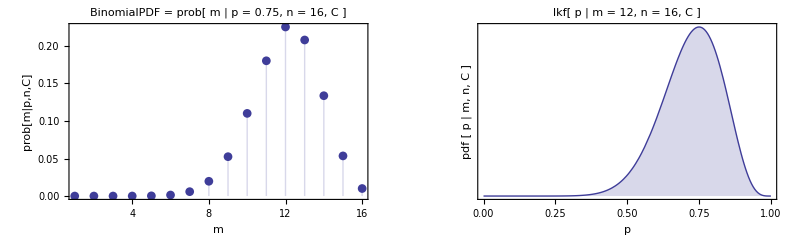

```mathematica
GraphicsRow[{pdfm,pdfp},ImageSize->11 72]
```

## Maximum Likelihood Estimate, p̂

### From the Posterior Likelihood Function

```mathematica
FindMaximum[ {p^12(1-p)^(16-12),0<p<1},{p,0.5}]
```

{0.000123736,{p→0.750068}}

{0.000123736,{p→0.750068}}

### From the Posterior Probability Distribution Function

```mathematica
FindMaximum[{((n+1)!)/(m! (n-m)!) p^m (1-p)^(n-m)/.{m->12,n->16},0<p<1},{p,0.5}]
```

{3.82838,{p→0.75}}

{3.82838,{p→0.75}}

Note the small size of LKF restricts the digital precision of Find Maximum

## Plot Confidence Interval v Credible Interval

```mathematica
Clear[pdfpo,cdfpo,p,m,n];
```

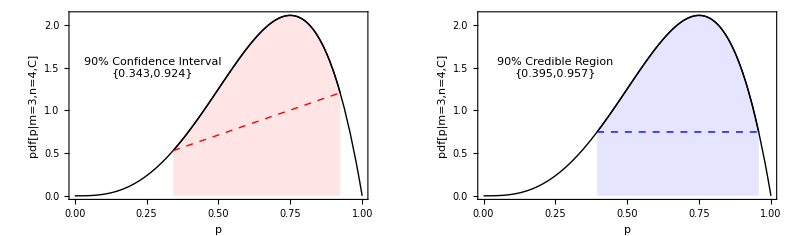

```mathematica
pdfpo[p_,m_,n_]=((n+1)!)/(m!(n-m)!)p^m(1-p)^(n-m);
cdfpo[p_,m_,n_]= ∫pdfpo[p,m,n]ⅆp;
Clear[p,lcl,ucl];Off[NSolve::ratnz];
coI={lcl,ucl}/.Flatten[{NSolve[{cdfpo[lcl,3,4]==0.05,0<lcl<1},lcl ,Reals],NSolve[{cdfpo[ucl,3,4]==0.95,0<ucl<1},ucl,Reals]}];
Clear[p,lo,hi];crI = {lo,hi}/.NSolve[{pdfpo[lo,3,4]==pdfpo[hi,3,4],cdfpo[hi,3,4]-cdfpo[lo,3,4]==0.9,0<lo<hi<1},{lo,hi},Reals]//Flatten;
p1=Plot[pdfpo[p,3,4],{p,0,1},PlotStyle->{Black,Thick},AxesOrigin->{0.75,0},Frame->True,FrameLabel-> {"p","pdf[p|m=3,n=4,C]","
StyleBox[OverscriptBox[\"p\", \"^\"],\nFontWeight->\"Plain\"]
StyleBox[\" \",\nFontWeight->\"Plain\"]
StyleBox[\"=\",\nFontWeight->\"Plain\"]
StyleBox[\" \",\nFontWeight->\"Plain\"]
StyleBox[\"0.75\",\nFontWeight->\"Plain\"]",""},BaseStyle->{FontFamily-> "Arial",14}];

p2=Plot[pdfpo[p,3,4],{p,l1=coI[[1]],l2=coI[[2]]},Filling->0,FillingStyle-> Opacity[0.1,Red],
PlotRange-> {0,Automatic},PlotStyle-> Black,
Epilog->{Red,Dashed,Line[{{l1,pdfpo[l1,3,4]},{l2,pdfpo[l2,3,4]}}]}  ];

p3=Plot[pdfpo[p,3,4],{p,l3=crI[[1]],l4=crI[[2]]},Filling->0,FillingStyle->Opacity[0.1,Blue],
PlotRange-> {0,Automatic},PlotStyle-> Black,
Epilog->{Blue,Dashed,Thick,Line[{{l3,pdfpo[l3,3,4]},{l4,pdfpo[l4,3,4]}}]}       ];

GraphicsRow[{
Show[p1,p2, Epilog->{Text[Column[{"90% Confidence Interval",Round[coI,0.001]}],{0.27,1.5}],
Red,Dashed,Thick,Line[{{l1,pdfpo[l1,3,4]},{l2,pdfpo[l2,3,4]}}],
}  ],
Show[p1,p3,Epilog->{Text[Column[{"90% Credible Region",Round[crI,0.001]}],{0.25,1.5}],
Blue,Dashed,Thick,Line[{{l3,pdfpo[l3,3,4]},{l4,pdfpo[l4,3,4]}}]}]
 },ImageSize-> 11 72   ]
```

## Bayesian Inference for Sequential Analysis

### Data from 2 experiments, #1 with 8 trials, #2 with 7 trials.

```mathematica
{data1 = {0, 0,1, 0,  1, 0, 0, 1},data2={0,1,0,0,0,0,0}};
{m1=3, m2=1,m12=m1+m2,n1=Length[data1],n2=Length[data2],n12=n1+n2};
```

### LKF[ p | m, n ] for experiments 1 and 2

```mathematica
Clear[n,m,p,pdf,pdf1,pdf2];
```

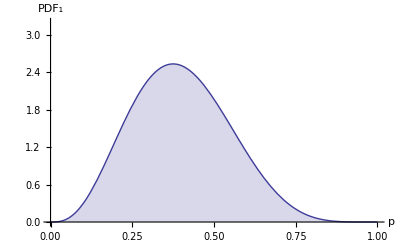
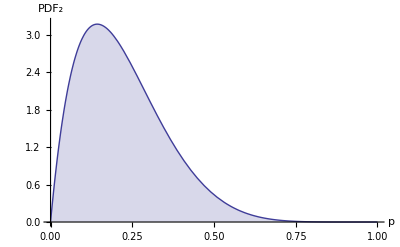
| Exp #1 | Exp #2
DATA | {0,0,1,0,1,0,0,1} | {0,1,0,0,0,0,0}
PDF | 504 (1-p)^5 p^3 | 56 (1-p)^6 p
Plots | -Graphics- | -Graphics-

```mathematica
pdf:=((n+1)!)/(m! (n-m)!) p^m (1-p)^(n-m)
{pdf1=pdf/.{m->m1,n->n1},pdf2=pdf/.{m->m2,n->n2}};
Row[{pl1=Plot[pdf1,{p,0,1},PlotRange-> {0,3.2},AxesLabel->{"p","PDF_1"},
BaseStyle->{FontFamily->"Arial",12},Filling->Axis],pl2= Plot[pdf2,{p,0,1},PlotRange-> {0,3.2},AxesLabel->{"p","PDF_2"},BaseStyle->{FontFamily->"Arial",12},Filling->Axis]
}]; 

Style[Framed[Grid[{{"","Exp #1", "Exp #2"},{"DATA",data1,data2},{"PDF",pdf1, pdf2},{"Plots",pl1, pl2}},
Dividers-> {{False,True},{False,True}},Spacings->{2,1}],RoundingRadius->8,FrameStyle-> {Thick},FrameMargins-> 8,ImageMargins-> 4],FontFamily-> "Helvetica", FontSize->18]
```

## PDF for experiments 1 and 2 Combined

### Sequential Analysis with pdf1 the prior for pdf2

```mathematica
pdf12 =(pdf2 pdf1)/(∫_0^1 pdf2 pdf1 ⅆp); Style[Row[{"pdf12 = (pdf2 *  pdf1)/(∫_0^1) = ",pdf12}],{16,FontFamily->Helv}]
```

pdf12 = (pdf2 pdf1)/(∫_0^1) = 21840 (1-p)^11 p^4

### Sequential = Combined Analysis with m = 4, n =15

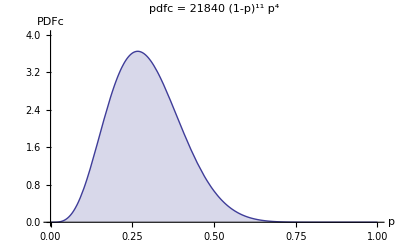

```mathematica
pdfc = pdf/.{m->4,n->15};
Plot[pdfc,{p,0,1},PlotRange-> {0,4},PlotStyle->Thick,AxesLabel->{"p","PDFc"},BaseStyle-> {16,FontFamily-> Helv},Filling->Axis,PlotLabel->Row[{"pdfc = ",pdfc}]]
```

## Deduction v Induction One last Time

-Graphics-

### On the Left, given p and n, deduce the probability of m ≤ n. Deductive Reasoning for Gambling and Insurance. Assumes p and n are real while data, m is uncertain.

### On the right, given data {m, n} infer the PDF[p | m, n, C] Inductive Reasoning for Education and Science. Assumes data are real while parameters are uncertain.

## Summary

### Bayesian Probability Theory is based on Common Sense When Quantified, This Common Sense uniquely gives 2 Axioms The 2 Axioms of probability theory are applied with Boolean Algebra plus Linear Algebra The 2 Axioms also produce useful tools for inference Bayes Rule, Marginal Integration and Evidence Today, a Binary Decision Experiment illustrated Bayesian Inference Uniform Priors in Bayes Rule yield Likelihood Functions Sequential Experiments are Valid